```mathematica
(* Sensitivity Ananlysis *)
(* Max   z=30x1+20x2
s.t. 2x1+x2≤8
	 x1+3x2≤8 *)

Maximize[{30 x1+20 x2,2 x1+x2≤8 && x1+3 x2≤8},{x1,x2}]
```

{128,{x1→16/5,x2→8/5}}

```mathematica
Maximize[{30 x1+20 x2,2 x1+x2≤9 && x1+3 x2≤8},{x1,x2}]
```

{142,{x1→19/5,x2→7/5}}

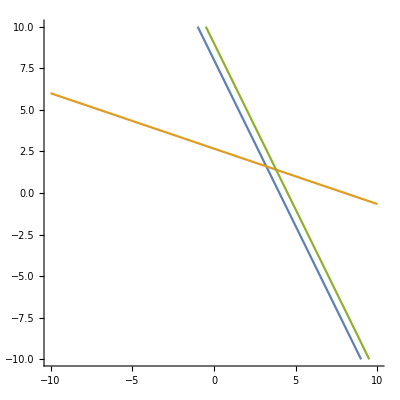

```mathematica
ContourPlot[{2 x1+x2==8,x1+3 x2==8,2 x1+x2==9},{x1,-10,10},{x2,-10,10},Frame->False,Axes->True]
```

```mathematica
(* Sensitivity Analysis
 Change of Objective
   Max z=35x1+25x2 *)
(* Constraints same as above *)

Maximize[{35 x1+25 x2,2 x1+x2≤8 && x1+3 x2≤8},{x1,x2}]
```

{152,{x1→16/5,x2→8/5}}

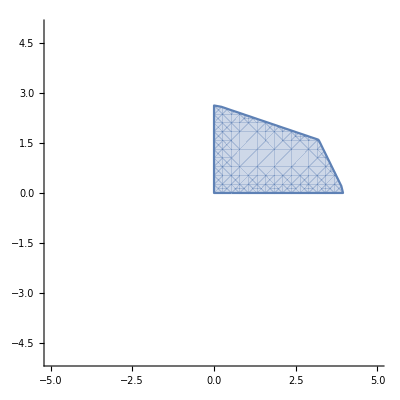

```mathematica
RegionPlot[{2 x1+x2 ≤8 && x1+3 x2≤8 && x1≥0 && x2≥0},{x1,-5,5},{x2,-5,5},Frame->False,Axes->True]
```